# Checking the absence of the inverted Marcus region in ET with quantum modes

## Units

Unit conversion factors:

```mathematica
bohr2a=0.529177`50;
a2bohr=1/bohr2a;
au2kcal=627.5095`50;
kcal2au=1/au2kcal;
ev2cm=8065.54477`50;
cm2ev = 1/ev2cm ;
au2ev=27.2113`50;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`50*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

Physical constants:

```mathematica
hbar=1;
ℏ=1;
hbarps=0.047685388`50/(au2kcal*π);
Dalton=1822.8900409014022`50;
MassH=1.0072756064562605`50;
MassD=2.0135514936645316`50;
MassT=3.0160492`50;
mH=MassH*Dalton;
mD=MassD*Dalton;
mT=MassT*Dalton;
kb=3.16683`50*10^-6;
```

### Accuracy settings

```mathematica
AccN=50;
```

## Parameters of the two-state ET model

Electronic coupling (kcal/mol):

```mathematica
V=0.03`50*ev2kcal
```

0.6918186562200262390991977597542197542932531705578

Bath reorganization energy (kcal/mol) :

```mathematica
λ=20;
```

Mass of the quantum mode:

```mathematica
Mass=5;
```

Frequencies of the quantum mode for the reactant and product proton potentials (cm^-1):

```mathematica
f1=2000.0`50;
f2=2000.0`50;
```

Minima of the reactant and product potentials (Å→ Bohr):

```mathematica
xm1=0;
xm2=-0.5`50*a2bohr;
```

Harmonic potentials (kcal/mol):

```mathematica
U1[x_,f_]:=au2kcal 1/2 Mass*Dalton*(f*cm2au)^2(x-xm1)^2;
U2[x_,f_]:=au2kcal 1/2 Mass*Dalton*(f*cm2au)^2(x+-xm2)^2;
```

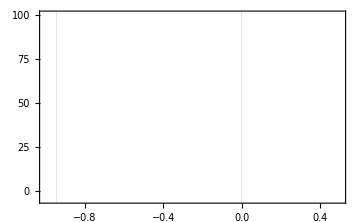

```mathematica
Plot[{U1[x],U2[x]},{x,-1,0.5},Axes->False,Frame->True,PlotStyle->{{Green,Dashed,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Red,AbsoluteThickness[1.0]}},PlotRange->{-5,100},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameStyle->AbsoluteThickness[1.0],ImageSize->Medium,GridLines->{{xm1,xm2},None}]
```

Temperature (K):

```mathematica
T=30;
β=1/(kb*T);
```

## Harmonic oscillator energies and wavefunction overlaps

Harmonic energy levels (kcal/mol):

```mathematica
HarmEnergy[n_,f_]:=Module[{omega},
omega=f*cm2au;
au2kcal*omega*(n+1/2)];
```

Harmonic wavefunctions:

```mathematica
HarmWavefunction[n_,f_,x_,OptionsPattern[{M->MassH}]]:=Module[{mu,o,wnorm,w1,w2,q},
mu=OptionValue[M]*Dalton;
o=f*cm2au;
wnorm=((mu*o)/π)^(1/4)*2^(-n/2)*(n!)^(-1/2);
w1=Exp[-1/2 mu*o*x^2];
q=x*Sqrt[mu*o];
w2=HermiteH[n,q];
wnorm*w1*w2];
```

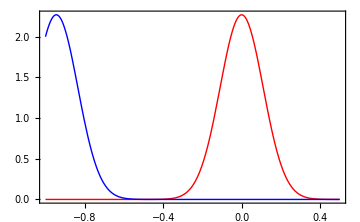

```mathematica
Plot[{HarmWavefunction[0,f1,x,M->Mass],HarmWavefunction[0,f2,x-xm2,M->Mass]},{x,-1,0.5},PlotRange->All,Axes->True,Frame->True,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[1.0],BaseStyle->{FontSize->16,FontFamily->"Helvetica"},ImageSize->Medium]
```

Overlap integrals (in this expression the first oscillator is d Bohr to the right of the second one):

```mathematica
HarmOverlap[n1_,n2_,f1_,f2_,d_,OptionsPattern[{M->MassH,Acc->120}]]:=Module[{mass,acc,o1,o2,mu,a1,a2,s,A,Prefactor,b1,b2,i,j,Kaux},
acc=OptionValue[Acc];
mass=SetAccuracy[OptionValue[M],acc];
Kaux[i_,j_,a_,b_]:=SetAccuracy[If[OddQ[i+j],0,(i+j-1)!!/(a+b)^((i+j)/2)],acc];
mu=SetAccuracy[mass*Dalton,acc];
o1=SetAccuracy[f1*cm2au,acc];
o2=SetAccuracy[f2*cm2au,acc];
a1=SetAccuracy[(mu*o1),acc];
a2=SetAccuracy[(mu*o2),acc];
s=SetAccuracy[(a1*a2*d^2)/(a1+a2),acc];
A=SetAccuracy[(2*Sqrt[a1*a2])/(a1+a2),acc];
Prefactor=SetAccuracy[Sqrt[(A*Exp[-s])/(2^(n1+n2)*n1!*n2!)],acc];
b1=SetAccuracy[-((d*a2*Sqrt[a1])/(a1+a2)),acc];
b2=SetAccuracy[(d*a1*Sqrt[a2])/(a1+a2),acc];
Prefactor*Sum[Binomial[n1,i]*Binomial[n2,j]*HermiteH[n1-i,b1]*HermiteH[n2-j,b2]*(2*Sqrt[a1])^i*(2*Sqrt[a2])^j*Kaux[i,j,a1,a2],{j,0,n2},{i,0,n1}]];
```

```mathematica
HarmOverlap[0,35,3000,3000,0.5a2bohr]
```

0.000083903784818063911063955148979686443797406244853010274647862491517212746004209720354830682148

```mathematica
Needs["BarCharts`"]
```

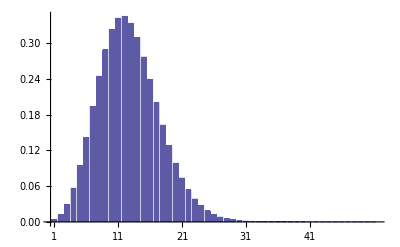

```mathematica
BarChart[Table[HarmOverlap[0,i,3000,3000,0.5a2bohr],{i,0,50,1}]]
```

## ET Rate constant

No Boltzmann distribution in the initial state: no thermal excitations

```mathematica
ket[dG_,f1_,f2_,nmax_,T_,OptionsPattern[{M->MassH}]]:=Module[{mass,omega1,omega2,lambda},
mass=OptionValue[M];
omega1=f1*cm2au;
omega2=f2*cm2au;
lambda=λ*kcal2au;
10^12*ps2au*Sqrt[π/(lambda*kb*T)]*(V*kcal2au)^2*
Sum[
HarmOverlap[0,i,f1,f2,xm1-xm2,M->mass]^2*Exp[-(dG*kcal2au+lambda+(HarmEnergy[i,f2]-HarmEnergy[0,f1])*kcal2au)^2/(4*lambda*kb*T)]
,{i,0,nmax,1}]
];
```

```mathematica
HarmOverlap[0,30,f1,f2,xm1-xm2,M->Mass]
```

0.1877750134486490138399763449135774981990090480727118783430041606244559431468041174012454127

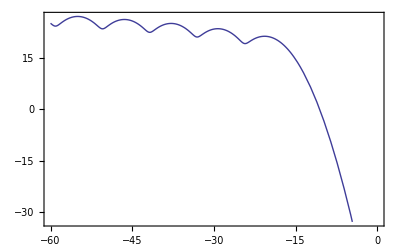

```mathematica
Plot[Log[ket[x,2500,3000,30,30,M->1]],{x,-60,0},Axes->False,Frame->True]
```

## Partition function and Boltzmann factors

```mathematica
Z[T_,n_]:=Module[{i},SetAccuracy[1+Sum[Exp[-kcal2au/(kb T)(HarmEnergy[i,f1]-HarmEnergy[0,f1])],{i,1,n}],50]];
```

```mathematica
P=Function[{T,i,n},SetAccuracy[1/Z[T,n] Exp[-kcal2au/(kb T)(HarmEnergy[i,f1]-HarmEnergy[0,f1])],50]];
```

```mathematica
P[300,1,20]
```

0.0000682804064867227418746869762482074370425119601

## Fixed R

```mathematica
V=SetAccuracy[1.0/au2kcal,AccN];
```

```mathematica
prefactor=SetAccuracy[10^12/au2ps,AccN];
```

```mathematica
RateRH[T_,Δ_,λ_,R_,i_,j_,f1_,f2_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=HarmOverlap[i,j,f1,f2,R];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+(HarmEnergy[j,f2]-HarmEnergy[0,f2]-HarmEnergy[i,f1]+HarmEnergy[0,f1])*kcal2au)^2/(4Λ);
A0*A1^2*A2*Exp[-Ea/(kb T)]];
```

```mathematica
V
```

0.0015936013717720608814237825967552453221287578344

```mathematica
RateRH[300,-10,20,0.1a2bohr,0,1,300,300]
```

1.223426998782660416988837653783401504319135368×10^11

```mathematica
TotalrateRH[T_,Δ_,λ_,R_,n_,m_,f1_,f2_]:=Module[{i,j},Sum[P[T,i,n]Sum[RateRH[T,Δ,λ,R,i,j,f1,f2],{j,0,m}],{i,0,n}]];
```

## High-T

```mathematica
αH[R_,i_,j_,f1_,f2_]:=Module[{h,a},
h=0.0001`50;
a=SetAccuracy[-1/(2h)(Log[HarmOverlap[i,j,f1,f2,R+h]]-Log[HarmOverlap[i,j,f1,f2,R-h]]),50];
Chop[a,10^-30]
];
```

```mathematica
αH[0.5a2bohr,1,11,3000,3000]
```

-115.2441719274959061492742051924462159158533230795308

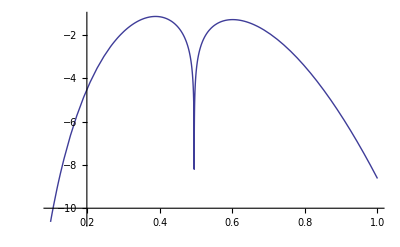

```mathematica
Plot[Log@Abs@HarmOverlap[1,11,3000,3000,x a2bohr],{x,0.1,1.0}]
```

```mathematica
-￿
```

-￿

```mathematica
%^2
```

￿^2

```mathematica
λaH=Function[{R,μ,i,j,f1,f2},SetAccuracy[(ℏ^2 αH[R,i,j,f1,f2]^2)/(2μ Dalton),120]];
```

```mathematica
Re@λaH[0.5a2bohr,100,0,0,3000,3000]au2kcal
```

0.24199256826933443040314509340701865174588459790375

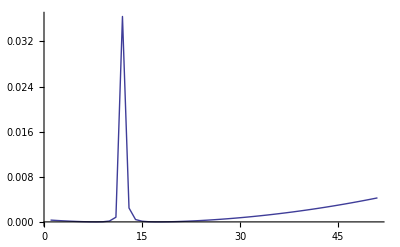

```mathematica
ListLinePlot[Table[Re@λaH[0.5a2bohr,100,1,i,3000,3000],{i,0,50}],PlotRange->All]
```

```mathematica
Clear[RateH6]
```

```mathematica
RateH6[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,f1_,f2_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea,S},
λα=Chop[λaH[R,μ,0,0,f1,f2],10^-30];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
S=HarmOverlap[i,j,f1,f2,R];
A0=prefactor*V^2*S^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=1/(4Λ)(dG+Λ+(HarmEnergy[j,f2]-HarmEnergy[0,f2]-HarmEnergy[i,f1]+HarmEnergy[0,f1])kcal2au)^2;
Chop[A0*A1*A2*Exp[-Ea/(kb T)],10^-20]];
```

```mathematica
RateH6[300,-200,20,0.5a2bohr,100,200,4,30,3000,3000]
```

0.00005504892138000639888233642762279100163812758249

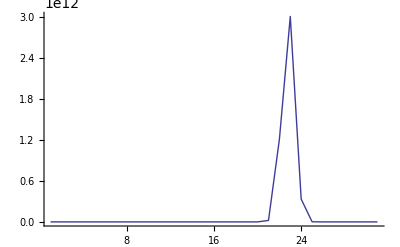

```mathematica
ListLinePlot[Table[RateH6[300,-200,20,0.5a2bohr,100,200,1,i,3000,3000],{i,0,30}],PlotRange->All]
```

```mathematica
TotalrateH6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_,f1_,f2_]:=Module[{i,j},Sum[P[T,i,n]Sum[RateH6[T,Δ,λ,R,μ,ω,i,j,f1,f2],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateH6[300,-200,20,0.5a2bohr,100,200,0,30,3000,3000]
```

8.931532418531288331146595066966546865934888274×10^11

```mathematica
TotalrateH6[300,-200,20,0.5a2bohr,100,200,10,29,3000,3000]
```

8.934046010961748946370328042310559599052822726×10^11

```mathematica
TotalrateH6[300,-330,20,0.5a2bohr,100,200,11,30,3000,3000]
```

5.59696377468673167071972757328720470811205233×10^-17

```mathematica
TotalrateH6[300,-200,20,0.5a2bohr,100,200,11,30,3000,3000]
```

```mathematica
TotalrateH6[300,-350,20,0.5a2bohr,100,200,9,27,3000,3000]
```

0

```mathematica
ListLinePlot[Table[TotalrateH6[300,-150,20,0.5a2bohr,100,200,0,i,3000,3000],{i,0,60}]]
```

-Graphics-

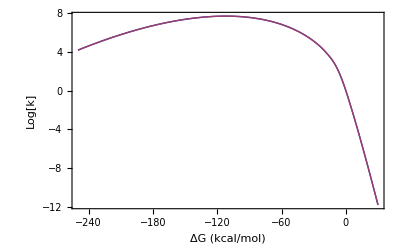

```mathematica
start=-250;finish=30;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateH6[300,dg,20,0.5a2bohr,100,200,10,28,3000,3000]/TotalrateH6[300,0,20,0.5a2bohr,100,200,10,28,3000,3000]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateH6[300,dg,20,0.5a2bohr,100,200,9,27,3000,3000]/TotalrateH6[300,0,20,0.5a2bohr,100,200,9,27,3000,3000]]},{dg,start,finish,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

```mathematica
start=-400;finish=1;step=1;
Export["test1.dat",Table[{dg,Log[10,TotalrateH6[300,dg,20,0.5a2bohr,100,200,17,80,3000,3000]/TotalrateH6[300,0,20,0.5a2bohr,100,200,17,80,3000,3000]]},{dg,start,finish,step}]]
```

test1.dat

## Overlap tests

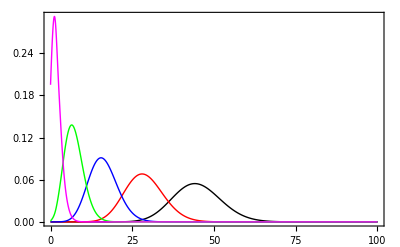

```mathematica
start=0;finish=100;step=1;μ=0;
Monitor[
ListLinePlot[
{Table[{x,HarmOverlap[μ,x,2500,3000,1.a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.8a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.6a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.4a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.2a2bohr]^2},{x,start,finish,step}]},PlotStyle->{Black,Red,Blue,Green,Magenta},Frame->True,Axes->False,
PlotRange->All,InterpolationOrder->4],
{"ν"->x,ProgressIndicator[Dynamic[x],{start,finish}]}]
```

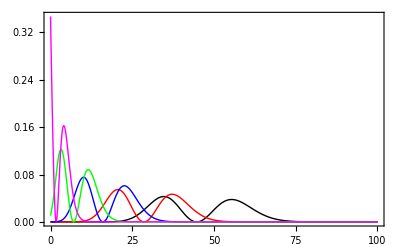

-Graphics-

-Graphics-

-Graphics-

```mathematica
start=0;finish=100;step=1;μ=1;
Monitor[
ListLinePlot[
{Table[{x,HarmOverlap[μ,x,2500,3000,1.a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.8a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.6a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.4a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.2a2bohr]^2},{x,start,finish,step}]},PlotStyle->{Black,Red,Blue,Green,Magenta},Frame->True,Axes->False,
PlotRange->All,InterpolationOrder->4],
{"ν"->x,ProgressIndicator[Dynamic[x],{start,finish}]}]
```

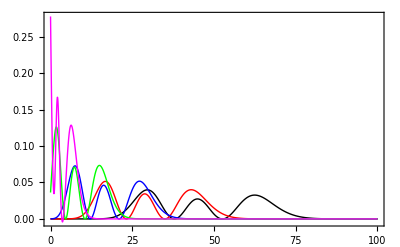

-Graphics-

-Graphics-

-Graphics-

```mathematica
start=0;finish=100;step=1;μ=2;
Monitor[
ListLinePlot[
{Table[{x,HarmOverlap[μ,x,2500,3000,1.a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.8a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.6a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.4a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.2a2bohr]^2},{x,start,finish,step}]},PlotStyle->{Black,Red,Blue,Green,Magenta},Frame->True,Axes->False,
PlotRange->All,InterpolationOrder->4],
{"ν"->x,ProgressIndicator[Dynamic[x],{start,finish}]}]
```

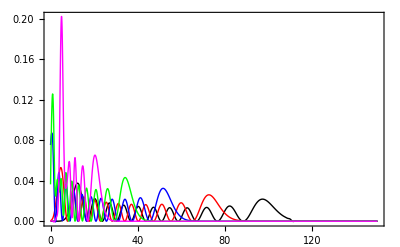

-Graphics-

-Graphics-

-Graphics-

```mathematica
start=0;finish=150;step=1;μ=10;
Monitor[
ListLinePlot[
{Table[{x,HarmOverlap[μ,x,2500,3000,1.a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.8a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.6a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.4a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,2500,3000,0.2a2bohr]^2},{x,start,finish,step}]},PlotStyle->{Black,Red,Blue,Green,Magenta},Frame->True,Axes->False,
PlotRange->All,InterpolationOrder->4],
{"ν"->x,ProgressIndicator[Dynamic[x],{start,finish}]}]
```

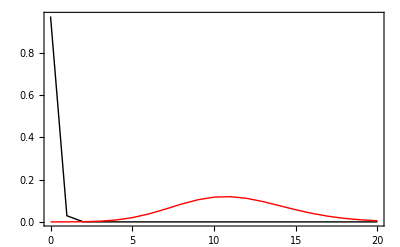

```mathematica
start=0;finish=20;step=1;μ=0;
Monitor[
ListLinePlot[
{Table[{x,HarmOverlap[μ,x,200,200,0.1a2bohr]^2},{x,start,finish,step}],Table[{x,HarmOverlap[μ,x,3000,3000,0.5a2bohr]^2},{x,start,finish,step}]},PlotStyle->{Black,Red,Blue,Green,Magenta},Frame->True,Axes->False,
PlotRange->All],
{"ν"->x,ProgressIndicator[Dynamic[x],{start,finish}]}]
```

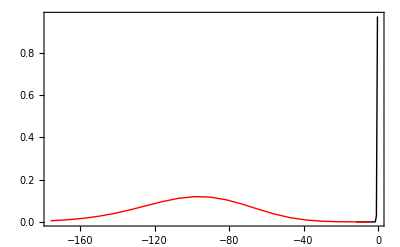

```mathematica
start=0;finish=20;step=1;μ=0;
Monitor[
ListLinePlot[
{Table[{-HarmEnergy[x,200],HarmOverlap[μ,x,200,200,0.1a2bohr]^2},{x,start,finish,step}],Table[{-HarmEnergy[x,3000],HarmOverlap[μ,x,3000,3000,0.5a2bohr]^2},{x,start,finish,step}]},PlotStyle->{Black,Red,Blue,Green,Magenta},Frame->True,Axes->False,
PlotRange->All],
{"ν"->x,ProgressIndicator[Dynamic[x],{start,finish}]}]
```

```mathematica
start=-200;finish=50;step=1;Monitor[Export["01.dat",Table[{-HarmEnergy[x,200],HarmOverlap[μ,x,200,200,0.1a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

01.dat

```mathematica
start=-200;finish=50;step=1;Monitor[Export["05.dat",Table[{-HarmEnergy[x,3000],HarmOverlap[μ,x,3000,3000,0.5a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

05.dat

```mathematica
start=-200;finish=50;step=1;Monitor[Export["01-2.dat",Table[{-HarmEnergy[x,200],HarmOverlap[1,x,200,200,0.1a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

01-2.dat

```mathematica
start=-200;finish=50;step=1;Monitor[Export["05-2.dat",Table[{-HarmEnergy[x,3000],HarmOverlap[1,x,3000,3000,0.5a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

05-2.dat

```mathematica
start=0;finish=30;step=1;Monitor[Export["01-3.dat",Table[{x,HarmOverlap[0,x,200,200,0.1a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

01-3.dat

```mathematica
start=0;finish=30;step=1;Monitor[Export["05-3.dat",Table[{x,HarmOverlap[0,x,3000,3000,0.5a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

05-3.dat

```mathematica
start=0;finish=30;step=1;Monitor[Export["01-4.dat",Table[{x,HarmOverlap[1,x,200,200,0.1a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

01-4.dat

```mathematica
start=0;finish=30;step=1;Monitor[Export["05-4.dat",Table[{x,HarmOverlap[1,x,3000,3000,0.5a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

05-4.dat

```mathematica
start=0;finish=50;step=1;Monitor[Export["01-5.dat",Table[{HarmEnergy[x,200],HarmOverlap[0,x,200,200,0.1a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

01-5.dat

```mathematica
start=00;finish=50;step=1;Monitor[Export["05-5.dat",Table[{HarmEnergy[x,3000],HarmOverlap[0,x,3000,3000,0.5a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

05-5.dat

```mathematica
start=0;finish=50;step=1;Monitor[Export["01-6.dat",Table[{HarmEnergy[x,200],HarmOverlap[1,x,200,200,0.1a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

01-6.dat

```mathematica
start=00;finish=50;step=1;Monitor[Export["05-6.dat",Table[{HarmEnergy[x,3000],HarmOverlap[1,x,3000,3000,0.5a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

05-6.dat

```mathematica
start=0;finish=80;step=1;Monitor[Export["01-7.dat",Table[{HarmEnergy[x,200],HarmOverlap[0,x,200,200,0.1a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

01-7.dat

```mathematica
start=0;finish=80;step=1;Monitor[Export["05-7.dat",Table[{HarmEnergy[x,3000],HarmOverlap[0,x,3000,3000,0.5a2bohr]^2},{x,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

05-7.dat

```mathematica
HarmOverlap[0,20,3000,3000,0.5a2bohr]^2
```

0.00543680844098519718757447256971942063406459924780292034724775223121316582751413088450675467312379313570013

## Rate tests

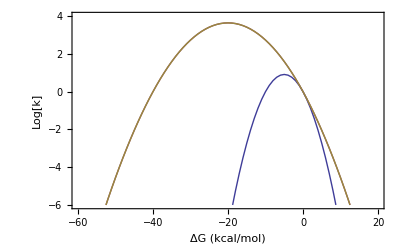

```mathematica
start=-60;finish=20;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,0,0,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,0,0,3000,3000]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.1a2bohr,0,0,200,200]/TotalrateRH[300,0,20,0.1a2bohr,0,0,200,200]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,0,0,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,0,0,3000,3000]]},{dg,start,finish,step}]]},Frame->True,Axes->False,PlotRange->{-6,4},
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

```mathematica
start=-200;finish=30;step=1;
Export["testa.dat",Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,0,0,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,0,0,3000,3000]],Log[10,TotalrateRH[300,dg,20,0.1a2bohr,0,0,200,200]/TotalrateRH[300,0,20,0.1a2bohr,0,0,200,200]],Log[10,TotalrateRH[300,dg,20,0.5a2bohr,0,0,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,0,0,3000,3000]]},{dg,start,finish,step}]]
```

test1.dat

```mathematica
TotalrateRH[300,-200,20,0.1a2bohr,7,15,300,300]
```

2.032151358596788613641347844434264701308700453×10^-273

```mathematica
TotalrateRH[300,-10,20,0.1a2bohr,5,6,300,300]
```

4.096790904033752773213763442037348241755737795×10^12

```mathematica
TotalrateRH[300,-10,20,0.1a2bohr,20,100,300,300]
```

«1»

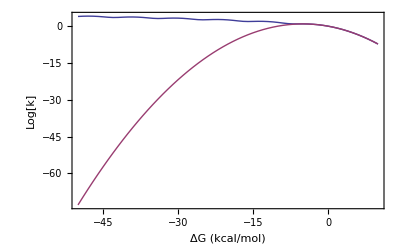

```mathematica
start=-50;finish=10;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,6,15,3000,3000]]},{dg,-50,10,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,0,0,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,0,0,3000,3000]]},{dg,-50,10,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

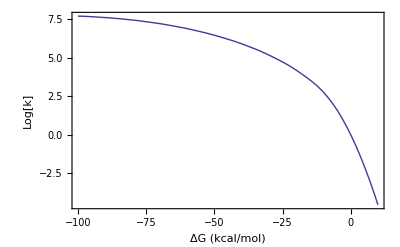

```mathematica
start=-100;finish=30;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,6,15,3000,3000]]},{dg,-100,10,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

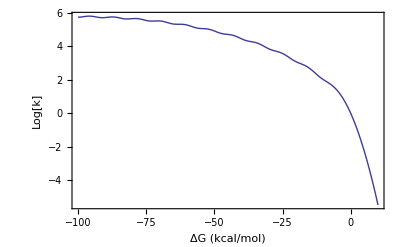

```mathematica
start=-100;finish=30;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,10,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,10,0.5a2bohr,6,15,3000,3000]]},{dg,-100,10,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

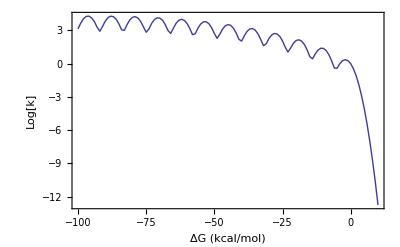

```mathematica
start=-100;finish=30;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,2,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,2,0.5a2bohr,6,15,3000,3000]]},{dg,-100,10,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

```mathematica
start=-150;finish=110;step=5;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.1a2bohr,6,15,200,200]/TotalrateRH[300,0,20,0.1a2bohr,6,15,200,200]]},{dg,start,finish,step}]]},
PlotStyle->{Red,Blue,Black,{Red,Dashed},{Blue,Dashed},{Black,Dashed}},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All,InterpolationOrder->4],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

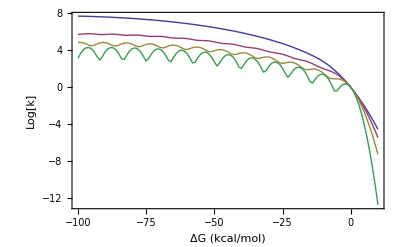

```mathematica
start=-100;finish=30;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,6,15,3000,3000]]},{dg,-100,10,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,10,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,10,0.5a2bohr,6,15,3000,3000]]},{dg,-100,10,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,6,15,3000,3000]]},{dg,-100,10,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,2,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,2,0.5a2bohr,6,15,3000,3000]]},{dg,-100,10,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

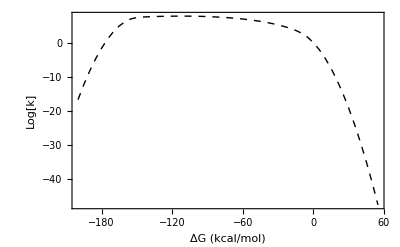

```mathematica
start=-200;finish=110;step=5;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,6,15,3000,3000]]},{dg,start,finish,step}]]},
PlotStyle->{Red,Blue,Black,{Red,Dashed},{Blue,Dashed},{Black,Dashed}},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All,InterpolationOrder->4],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

```mathematica
start=-200;finish=110;step=5;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,6,15,3000,3000]]},{dg,start,finish,step}]]},PlotRange->{-200,50}
PlotStyle->{Red,Blue,Black,{Red,Dashed},{Blue,Dashed},{Black,Dashed}},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All,InterpolationOrder->4],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

ListLinePlot::ioproc: {-100, -« 79 »}{-95, -« 79 »}{-90, -« 79 »}{-85, -« 79 »}« 3 »{-65, « 1 »}{-60, -« 79 »}{-55, -« 79 »}« 13 » may contain non-machine precision numbers, complex numbers, or invalid entries.

ListLinePlot::ioproc: {-100, -« 80 »}{-95, -« 79 »}{-90, -« 78 »}{-85, -« 79 »}« 3 »{-65, « 1 »}{-60, -« 79 »}{-55, -« 78 »}« 13 » may contain non-machine precision numbers, complex numbers, or invalid entries.

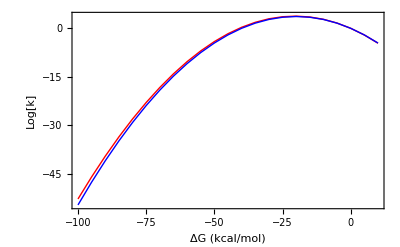

```mathematica
start=-100;finish=10;step=5;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,6,15,200,200]/TotalrateRH[300,0,20,0.5a2bohr,6,15,200,200]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.1a2bohr,6,15,200,200]/TotalrateRH[300,0,20,0.1a2bohr,6,15,200,200]]},{dg,start,finish,step}]]},
PlotStyle->{Red,Blue,Black,{Red,Dashed},{Blue,Dashed},{Black,Dashed}},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All,InterpolationOrder->4],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

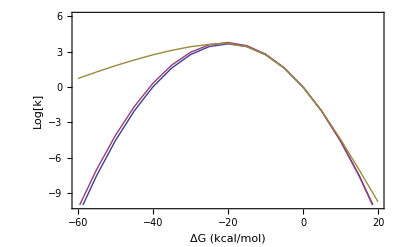

```mathematica
start=-60;finish=20;step=5;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.1a2bohr,6,15,200,200]/TotalrateRH[300,0,20,0.1a2bohr,6,15,200,200]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,6,15,200,200]/TotalrateRH[300,0,20,0.5a2bohr,6,15,200,200]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.1a2bohr,6,15,3000,3000]/TotalrateRH[300,0,20,0.1a2bohr,6,15,3000,3000]]},{dg,start,finish,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},PlotRange->{-10,4},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

```mathematica
start=-600;finish=20;step=.5;
Export["testb.dat",Table[{dg,Log[10,TotalrateRH[300,dg,20,0.1a2bohr,17,80,200,200]/TotalrateRH[300,0,20,0.1a2bohr,17,80,200,200]],Log[10,TotalrateRH[300,dg,20,0.5a2bohr,17,80,200,200]/TotalrateRH[300,0,20,0.5a2bohr,17,80,200,200]],Log[10,TotalrateRH[300,dg,20,0.1a2bohr,17,80,3000,3000]/TotalrateRH[300,0,20,0.1a2bohr,17,80,3000,3000]]},{dg,start,finish,step}]]
```

$Aborted

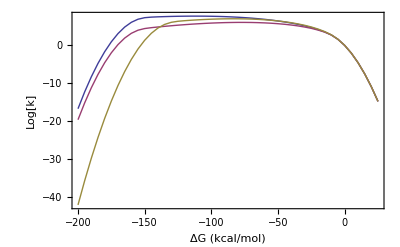

```mathematica
start=-600;finish=20;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,17,80,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,17,80,3000,3000]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.4a2bohr,17,80,3000,3000]/TotalrateRH[300,0,20,0.4a2bohr,17,80,3000,3000]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,17,80,2500,2500]/TotalrateRH[300,0,20,0.5a2bohr,17,80,2500,2500]]},{dg,start,finish,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

```mathematica
start=-400;finish=1;step=1;
Monitor[Export["testc.dat",Table[{dg,,Log[10,TotalrateRH[300,dg,20,0.4a2bohr,17,80,3000,3000]/TotalrateRH[300,0,20,0.4a2bohr,17,80,3000,3000]],Log[10,TotalrateRH[300,dg,20,0.5a2bohr,17,80,2500,2500]/TotalrateRH[300,0,20,0.5a2bohr,17,80,2500,2500]]},{dg,start,finish,step}]],{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

testc.dat

### PT

```mathematica
start=-200;finish=50;step=1;Monitor[Export["PT.dat",Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,6,15,3000,3000]]},{dg,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

PT.dat

### ET

```mathematica
start=-200;finish=50;step=1;Monitor[Export["ET.dat",Table[{dg,Log[10,TotalrateRH[300,dg,20,0.1a2bohr,6,15,200,200]/TotalrateRH[300,0,20,0.1a2bohr,6,15,200,200]]},{dg,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

ET.dat

### PCET

```mathematica
start=-200;finish=50;step=1;Monitor[Export["PCET.dat",Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,6,15,3000,3000]]},{dg,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

PCET.dat

### lambda=10

```mathematica
start=-100;finish=30;step=1;Monitor[Export["l10.dat",Table[{dg,Log[10,TotalrateRH[300,dg,10,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,10,0.5a2bohr,6,15,3000,3000]]},{dg,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

l10.dat

### lambda=2.5

```mathematica
start=-100;finish=30;step=0.5;Monitor[Export["l2.dat",Table[{dg,Log[10,TotalrateRH[300,dg,2.5,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,2.5,0.5a2bohr,6,15,3000,3000]]},{dg,start,finish,step}]],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

l2.dat

```mathematica
TotalrateRH[300,-300,5,0.5a2bohr,0,15,3000,3000]
```

6.23072990056566399546102391256095175946972712×10^-996

```mathematica
TotalrateRH[300,-300,5,0.5a2bohr,0,43,3000,3000]
```

623832.4548451938285909270301709130934898042109

```mathematica
TotalrateRH[300,-200,5,0.5a2bohr,6,15,3000,3000]
```

1.97386206392888602428102480871828495094041881×10^-148

```mathematica
TotalrateRH[300,-400,5,0.5a2bohr,13,45,3000,3000]
```

0.001405607384140795183064364313400828288176415368

```mathematica
TotalrateRH[300,-400,5,0.5a2bohr,14,50,3000,3000]
```

0.309394058693467789868731798088919510705694147

```mathematica
TotalrateRH[300,-400,5,0.5a2bohr,15,60,3000,3000]
```

0.3093940586934680390930438016849228267318

```mathematica
TotalrateRH[300,-400,5,0.5a2bohr,16,70,3000,3000]
```

0.309394058693468039093043801684922826732

```mathematica
TotalrateRH[300,-500,5,0.5a2bohr,14,50,3000,3000]
```

4.72335798338035748179014783851421014427159849×10^-163

```mathematica
TotalrateRH[300,-500,5,0.5a2bohr,17,80,3000,3000]
```

2.36581711179664697102771799952528132×10^-9

```mathematica
TotalrateRH[300,-500,5,0.5a2bohr,18,90,3000,3000]
```

2.36581711179664697102771799952528132×10^-9

```mathematica
TotalrateRH[300,-600,5,0.5a2bohr,17,80,3000,3000]
```

6.1511975105622418631190894792721131813×10^-18

```mathematica
TotalrateRH[300,-600,5,0.5a2bohr,18,90,3000,3000]
```

6.151197510562241863119089479272113×10^-18

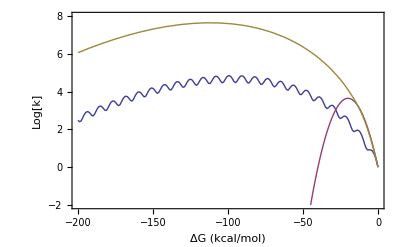

```mathematica
start=-200;finish=00;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,10,27,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,10,27,3000,3000]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.1a2bohr,10,27,200,200]/TotalrateRH[300,0,20,0.1a2bohr,10,27,200,200]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,10,27,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,10,27,3000,3000]]},{dg,start,finish,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},PlotRange->{-2,8},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

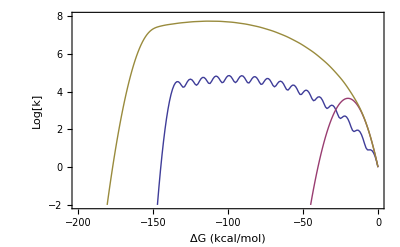

```mathematica
start=-200;finish=00;step=1;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,0,15,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,0,15,3000,3000]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.1a2bohr,0,15,200,200]/TotalrateRH[300,0,20,0.1a2bohr,0,15,200,200]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,0,15,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,0,15,3000,3000]]},{dg,start,finish,step}]]},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},PlotRange->{-2,8},
PlotRange->All],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

```mathematica
start=-600;finish=10;step=1;
Export["testa-2.dat",Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,0,80,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,0,80,3000,3000]],Log[10,TotalrateRH[300,dg,20,0.1a2bohr,0,80,200,200]/TotalrateRH[300,0,20,0.1a2bohr,0,80,200,200]],Log[10,TotalrateRH[300,dg,20,0.5a2bohr,0,80,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,0,80,3000,3000]]},{dg,start,finish,step}]]
```

testa-2.dat

```mathematica
start=-400;finish=1;step=1;
Monitor[Export["fig2.dat",Table[{dg,Log[10,TotalrateRH[300,dg,5,0.5a2bohr,17,80,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,17,80,3000,3000]],Log[10,TotalrateRH[300,dg,20,0.1a2bohr,17,80,200,200]/TotalrateRH[300,0,20,0.1a2bohr,17,80,200,200]],Log[10,TotalrateRH[300,dg,20,0.5a2bohr,17,80,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,17,80,3000,3000]]},{dg,start,finish,step}]],{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

```mathematica
start=-600;finish=10;step=1;
Export["fig5.dat",Table[{dg,Log[10,TotalrateRH[300,dg,2.5,0.5a2bohr,17,80,3000,3000]/TotalrateRH[300,0,2.5,0.5a2bohr,17,80,3000,3000]],Log[10,TotalrateRH[300,dg,5,0.5a2bohr,17,80,3000,3000]/TotalrateRH[300,0,5,0.5a2bohr,17,80,3000,3000]],Log[10,TotalrateRH[300,dg,10,0.5a2bohr,17,80,3000,3000]/TotalrateRH[300,0,10,0.5a2bohr,17,80,3000,3000]],Log[10,TotalrateRH[300,dg,20,0.5a2bohr,17,80,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,17,80,3000,3000]]},{dg,start,finish,step}]]
```

## Marcus parabolas (kcal/mol)

```mathematica
λ=5
```

20

```mathematica
GR[x_,i_]:=1/(4λ)(x+20)^2+HarmEnergy[i,3000];
```

```mathematica
GP[x_,i_]:=1/(4λ)(x-20)^2+HarmEnergy[i,3000];
```

```mathematica
GRD[x_,i_]:=1/(4λ)(x+20)^2+HarmEnergy[i,3000];
```

```mathematica
GPD[x_,i_]:=1/(4λ)(x-20)^2+HarmEnergy[i,3000];
```

```mathematica
Manipulate[Plot[{GR[x,0],GP[x,0]+ΔG,GR[x,1],GP[x,1]+ΔG,GR[x,2],GP[x,2]+ΔG,GR[x,3],GP[x,3]+ΔG},{x,-4λ,4λ},PlotStyle->{{Blue,Thick},{Red,Thick}},PlotRange->{-10,60},Axes->False,Frame->True,FrameLabel->{"Energy gap (kcal/mol)","Free energy (kcal/mol)"},AspectRatio->0.75,LabelStyle->Directive[FontFamily->"Arial", 20]],{ΔG,-30},LabelStyle->{Italic}]
```

```mathematica
Export["marcus1.dat",Table[{x,GRD[x,0],GPD[x,0]+10,GPD[x,1]+10,GPD[x,2]+10},{x,-4λ,4λ,0.2λ}]]
```

marcus1.dat

```mathematica
Export["marcus3.dat",Table[{x,GRD[x,0],GPD[x,0]-25,GPD[x,1]-25,GPD[x,2]-25},{x,-4λ,4λ,0.2λ}]]
```

marcus3.dat

## WF figure

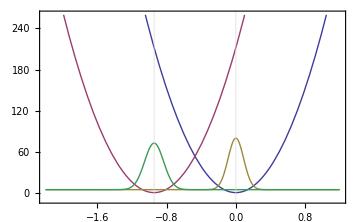

```mathematica
Plot[{U1[x],U2[x],30*HarmWavefunction[0,3000,x,M->Mass]+HarmEnergy[0,3000],30*HarmWavefunction[0,f2,x-xm2,M->Mass]+HarmEnergy[0,3000]},{x,-2.2,1.2},
PlotRange->{-10,260},Axes->False,Frame->True,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameStyle->AbsoluteThickness[1.0],ImageSize->Medium,GridLines->{{xm1,xm2},None}]
```

```mathematica
Export["harm.dat",Table[{x,U1[x,3000],U2[x,3000]},{x,-3.5,1.5,0.005}]]
```

harm.dat

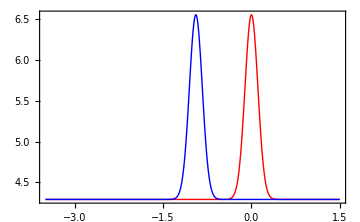

```mathematica
Plot[{HarmWavefunction[0,f1,x,M->Mass]+HarmEnergy[0,3000],HarmWavefunction[0,f2,x-xm2,M->Mass]+HarmEnergy[0,3000]},{x,-3.5,1.5},PlotRange->All,Axes->True,Frame->True,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[1.0],BaseStyle->{FontSize->16,FontFamily->"Helvetica"},ImageSize->Medium]
```

```mathematica
Export["020.dat",Table[{x,7*HarmWavefunction[0,3000,x,M->Mass]+HarmEnergy[20,3000],7*HarmWavefunction[20,3000,x-xm2,M->Mass]+HarmEnergy[20,3000]},{x,-3,1.5,.0005}]]
```

020.dat

```mathematica
"020.dat"
```

020.dat

```mathematica
Export["020.dat",Table[{x,U1[x],U2[x]+HarmEnergy[20,3000]-HarmEnergy[0,3000],30*HarmWavefunction[20,3000,x,M->Mass]+HarmEnergy[20,3000],30*HarmWavefunction[0,f2,x-xm2,M->Mass]+HarmEnergy[20,3000]},{x,-3,3,0.0005}]]
```

020.dat

```mathematica
Export["000.dat",Table[{x,U1[x],U2[x],30*HarmWavefunction[0,3000,x,M->Mass]+HarmEnergy[0,3000],30*HarmWavefunction[0,f2,x-xm2,M->Mass]+HarmEnergy[0,3000]},{x,-3,3,0.0005}]]
```

000.dat

```mathematica
Export["010.dat",Table[{x,U1[x],U2[x]+HarmEnergy[10,3000]-HarmEnergy[0,3000],30*HarmWavefunction[10,3000,x,M->Mass]+HarmEnergy[10,3000],30*HarmWavefunction[0,f2,x-xm2,M->Mass]+HarmEnergy[10,3000]},{x,-3,3,0.0005}]]
```

010.dat

```mathematica
HarmOverlap[0,0,3000,3000,0.5a2bohr]^2
```

0.0000136259202676053031908444044452354991419340797842438438528499740320047379714402767294785493568002738784896881793640829

```mathematica
HarmOverlap[0,10,3000,3000,0.5a2bohr]^2
```

0.1169914740485097346410884398131250155541107324578978082238831456477736113430334216011253181739073047997526141874

```mathematica
HarmOverlap[0,20,3000,3000,0.5a2bohr]^2
```

0.00543680844098519718757447256971942063406459924780292034724775223121316582751413088450675467312379313570013

## 2 modes

```mathematica
Z[T_,n_]:=Module[{i},SetAccuracy[1+Sum[Exp[-1/(kb T)(HarmEnergy[i,f1]-HarmEnergy[0,f1])],{i,1,n}],50]];
```

```mathematica
P=Function[{T,i,n},SetAccuracy[1/Z[T,n] Exp[-1/(kb T)(HarmEnergy[i,f1]-HarmEnergy[0,f1])],50]];
```

```mathematica
V=SetAccuracy[1.0/au2kcal,AccN];
```

```mathematica
prefactor=SetAccuracy[10^12/au2ps,AccN];
```

```mathematica
Rate2modes[T_,Δ_,λ_,R1_,R2_,i_,j_,k_,f1_,f2_,f3_,f4_]:=Module[{A0,A1,A2,A3,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=HarmOverlap[i,j,f1,f2,R1];
A2=HarmOverlap[i,k,f3,f4,R2];
A3=√(π/(kb T Λ));
Ea=1/(4Λ)(dG+Λ+((HarmEnergy[j,f2]-HarmEnergy[0,f2]-HarmEnergy[i,f1]+HarmEnergy[0,f1])(HarmEnergy[k,f4]-HarmEnergy[0,f4]-HarmEnergy[i,f3]+HarmEnergy[0,f3]))*kcal2au)^2;
A0*A1^2*A2^2*A3*Exp[-Ea/(kb T)]];
```

```mathematica
Totalrate2modes[T_,Δ_,λ_,R1_,R2_,n_,m_,o_,f1_,f2_,f3_,f4_]:=Module[{i,j,k},Sum[P[T,i,n]Sum[Rate2modes[T,Δ,λ,R1,R2,i,j,k,f1,f2,f3,f4],{k,0,o},{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrate2modes[300,-10,20,0.5a2bohr,0.0a2bohr,0,0,0,3000,3000,200,200]
```

5.661136613525356501764831548374662580129875597×10^7

```mathematica
Totalrate2modes[300,-10,20,0.5a2bohr,0.1a2bohr,1,1,1,3000,3000,200,200]
```

6.735854652463712871090611508745109858284344399×10^8

```mathematica
TotalrateRH[300,-10,20,0.5a2bohr,0,0,3000,3000]
```

5.661136613525356501764831548374662580129875597×10^7

ListLinePlot::ioproc: {-100, 7.6943888027720108183372626830169857345376137706202801884282`43.3942872735636}« 9 »« 13 » may contain non-machine precision numbers, complex numbers, or invalid entries.

ListLinePlot::ioproc: {-100, « 79 »}{-95, « 79 »}{-90, « 78 »}{-85, « 78 »}« 1 »« 1 »« 1 »{-65, « 77 »}{-60, « 78 »}{-55, « 78 »}« 13 » may contain non-machine precision numbers, complex numbers, or invalid entries.

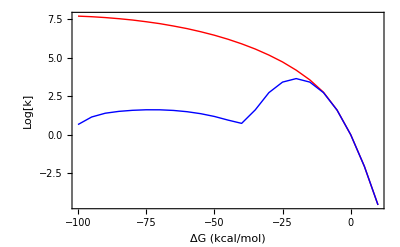

```mathematica
start=-100;finish=10;step=5;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,6,15,3000,3000]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,Totalrate2modes[300,dg,20,0.5a2bohr,0.1a2bohr,6,15,15,3000,3000,200,200]/Totalrate2modes[300,0,20,0.5a2bohr,0.1a2bohr,6,15,15,3000,3000,200,200]]},{dg,start,finish,step}]]},
PlotStyle->{Red,Blue,Black,{Red,Dashed},{Blue,Dashed},{Black,Dashed}},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All,InterpolationOrder->4],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

```mathematica
Totalrate2modes[300,-100,20,0.5a2bohr,0.1a2bohr,6,15,15,3000,3000,200,200]
```

3.070667401936836738642998231627967153280159129×10^10

```mathematica
Totalrate2modes[300,-100,20,0.5a2bohr,0.5a2bohr,7,16,16,3000,3000,200,200]
```

1.320220791151455008877212485991814548739932573×10^12

```mathematica
Totalrate2modes[300,-100,20,0.5a2bohr,0.5a2bohr,8,17,17,3000,3000,200,200]
```

1.569208771991749276930349076658706664808642033×10^12

```mathematica
Totalrate2modes[300,-100,20,0.5a2bohr,0.5a2bohr,9,18,18,3000,3000,200,200]
```

1.615879584935027127082138164794266206805320948×10^12

```mathematica
Totalrate2modes[300,-100,20,0.5a2bohr,0.5a2bohr,10,20,20,3000,3000,200,200]
```

1.618901584794459249041833978605894866919239081×10^12

```mathematica
Totalrate2modes[300,-100,20,0.5a2bohr,0.5a2bohr,10,20,20,3000,3000,200,200]
```

1.618969369280351688242396942255328127112423328×10^12

ListLinePlot::ioproc: {-100, 7.6943888027720108183372626830169857345376137706202801884282`43.3942872735636}« 9 »« 13 » may contain non-machine precision numbers, complex numbers, or invalid entries.

ListLinePlot::ioproc: {-100, 1.0956352574402482251537736472719113614205972693337827753927`46.79673975903201}« 9 »« 13 » may contain non-machine precision numbers, complex numbers, or invalid entries.

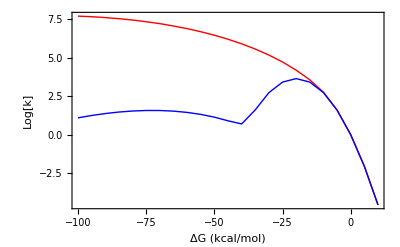

```mathematica
start=-100;finish=10;step=5;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateRH[300,dg,20,0.5a2bohr,6,15,3000,3000]/TotalrateRH[300,0,20,0.5a2bohr,6,15,3000,3000]]},{dg,start,finish,step}]],Tooltip[Table[{dg,Log[10,Totalrate2modes[300,dg,20,0.5a2bohr,0.1a2bohr,10,20,20,3000,3000,200,200]/Totalrate2modes[300,0,20,0.5a2bohr,0.1a2bohr,10,20,20,3000,3000,200,200]]},{dg,start,finish,step}]]},
PlotStyle->{Red,Blue,Black,{Red,Dashed},{Blue,Dashed},{Black,Dashed}},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All,InterpolationOrder->4],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```